## Adiabatic Gravitational Waveforms (Weak-field) in Schwarzschild - de Sitter

In this notebook we show the plots of gravitational waveforms for compact objects around Schwarzschild black holes influenced by an SdS parameter λ (y in this notebook). Results of this notebook has been used in Villanueva, John Adrian N., and Ian Vega. “Extreme-mass ratio inspirals in Schwarzschild-de Sitter spacetime: Weak-field orbits.” . https://journals.aps.org/prd/pdf/10.1103/npk4-61t8

The waveform polarizations are obtained using numerical kludge by

-Graphics-

With the quadrupolar moment as

-Graphics-

The derivatives in Q translate to derivatives in r(ψ) which uses the solutions of the weak field orbital evolution, included in this repository

#### Preamble

```mathematica
Exit[]
```

```mathematica
ClearAll["Global"]
```

```mathematica
plotsFolder=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plots"}]; (*automatically saves to the plots folder in the repo*)

Get["MaTeX`"];(*MaTeX for plot generation*)
SetOptions[MaTeX,FontSize->19,"Preamble"->{"\\usepackage{newtxtext,newtxmath}"},Magnification->1.2];
style=Directive[FontFamily->"Times",FontSize->23,Black];
```

### Orbital trajectories from the WFSDSORB package

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Pulling up the package

```mathematica
<<"../source/WFSDSOrbits.wl"
```

#### Main orbit solver and plotter

```mathematica
?wfsdsorb
```

```mathematica
?sol
```

Sample orbit, p=50, e=0.7, λ=10^-7 up to t=30000

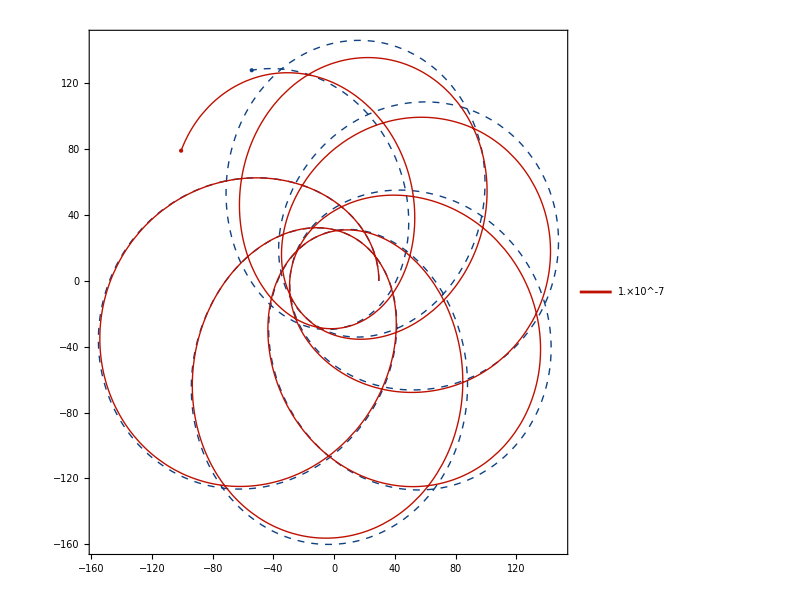

```mathematica
wfsdsorb[50,0.7,10^-7,30000]
```

One could also explicitly compute the coordinates of the EMRI in x-y plane

```mathematica
{?xpos,?ypos}
```

{,}

```mathematica
{xpos[t],ypos[t]}
```

{(Cos[f[t]+δ[t]] p[t])/(1+Cos[f[t]] e[t]),(p[t] Sin[f[t]+δ[t]])/(1+Cos[f[t]] e[t])}

One could then build the polarizations from the coordinates, e.g. h_+~(Q^(..))_11-(Q^(..))_22 ~ (x^(..))^2-(y^(..))^2 with radiation reaction substituted from the orbital evolution solvers

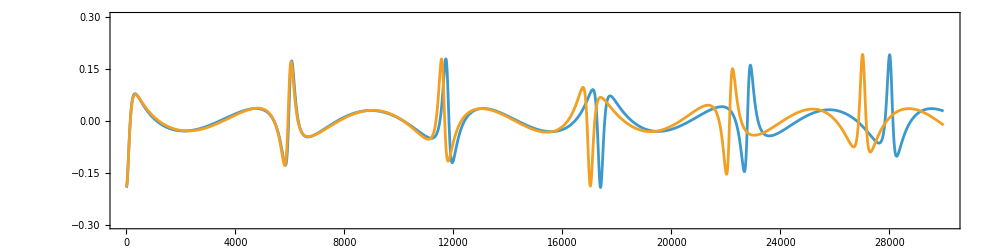

```mathematica
Plot[{Evaluate[D[xpos[x]^2-ypos[x]^2,{x,2}]/.sol[50,0.7,0]],Evaluate[D[xpos[x]^2-ypos[x]^2,{x,2}]+2(√(10^-7))/3 D[xpos[x]^2-ypos[x]^2,{x,1}]/.sol[50,0.7,10^-7]]},{x,0,30000},ImageSize->1000,Frame->True,AspectRatio->1/4,PlotRange->{Automatic,{-0.3,0.3}},LabelStyle->style,Frame->True,FrameLabel->{MaTeX["t"],MaTeX["h"]},PlotLegends->Placed[{MaTeX["h_+"],MaTeX["h_\\times"]},{Left,Bottom}]]
```

We can then build functions for the polarizations

```mathematica
hplus[x0_]:=Evaluate[D[xpos[t]^2-ypos[t]^2,{t,2}]]/.t->x0
hcross[x0_]:=Evaluate[D[2xpos[t]ypos[t],{t,2}]]/.t->x0
hplusSdS[y_,x0_]:=Evaluate[D[xpos[t]^2-ypos[t]^2,{t,2}]]+2 √y D[xpos[t]^2-ypos[t]^2,{t,1}]/.t->x0
hcrossSdS[y_,x0_]:=Evaluate[D[2xpos[t]ypos[t],{t,2}]]+2(√y)/3 D[2xpos[t]ypos[t],{t,1}]/.t->x0
```

We can also build a function for the polarizations for a given orbital parameter

```mathematica
hplusdata[p0_,e0_,y_,tf0_]:=Table[{Evaluate[hplus[x]/.sol[p0,e0,y]],Evaluate[hcross[x]/.sol[p0,e0,y]],x},{x,0,tf0}]
```

```mathematica
hplusdata[50,0.7,10^-7,100];
```

#### Plotters

```mathematica
?wfsdsgwplot
```

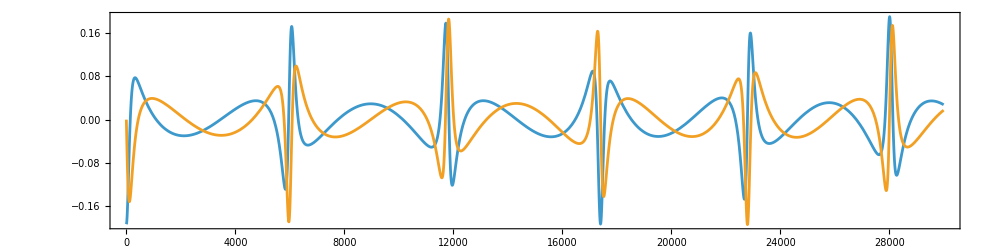

```mathematica
wfsdsgwplot[p0_,e0_,y0_,tf0_]:=Module[{tf,p,e,y},
p=p0;
e=p0;
y=y0;
tf=tf0;
Plot[{Evaluate[hplus[t]/.sol[p0,e0,0]],Evaluate[hcross[t]/.sol[p0,e0,0]]},{t,0,tf0},Frame->True,AspectRatio->1/4,ImageSize->1000,PlotRange->{Automatic,Full},LabelStyle->style,Frame->True,FrameLabel->{MaTeX["t"],MaTeX["h"]},PlotLegends->Placed[{MaTeX["h_+"],MaTeX["h_\\times"]},{Left,Bottom}]]]
wfsdsgwplot[50,0.7,10^-7,30000]
```

```mathematica
?wfsdsgwplusplot
```

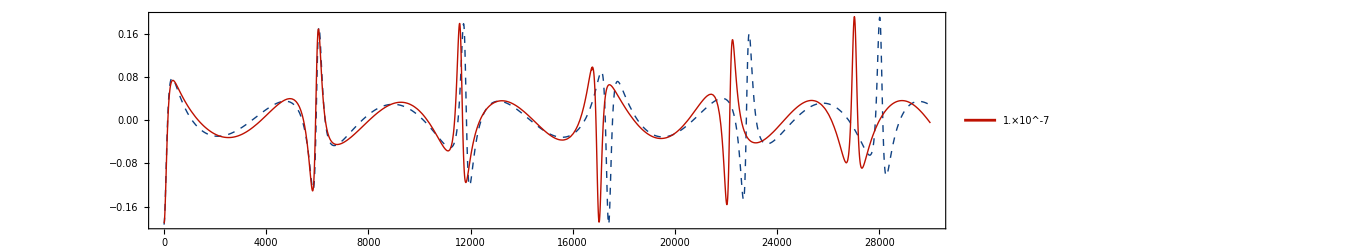

```mathematica
wfsdsgwplusplot[p0_,e0_,y0_,tf0_]:=Module[{tf,p,e,y},
p=p0;
e=p0;
y=y0;
tf=tf0;
Plot[{Evaluate[hplus[t]/.sol[p0,e0,0]],Evaluate[hplusSdS[y,t]/.sol[p0,e0,y]]},{t,0,tf0},Frame->True,AspectRatio->1/4,ImageSize->1000,PlotRange->{Automatic,Full},LabelStyle->style,Frame->True,FrameLabel->{MaTeX["t"],MaTeX["h_+"]},PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda="]TraditionalForm[y0//N]},{Left,Bottom}]]]
wfsdsgwplus=wfsdsgwplusplot[50,0.7,10^-7,30000]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"plus_50_7_-7.pdf"}];
Export[exportPath,wfsdsgwplus];
```

```mathematica
?wfsdsgwcrossplot
```

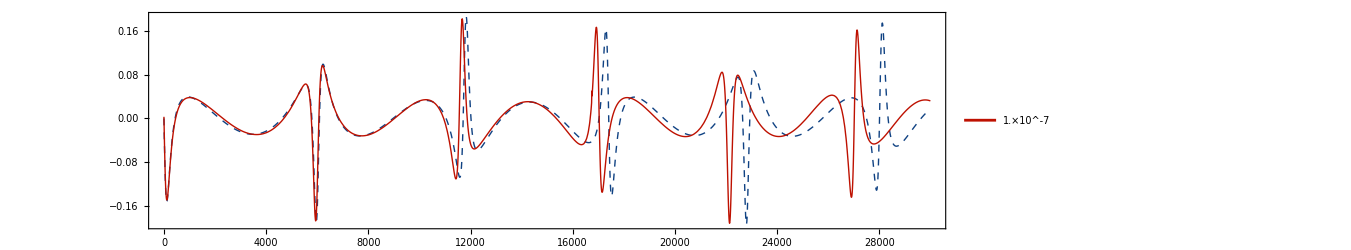

```mathematica
wfsdsgwcrossplot[p0_,e0_,y0_,tf0_]:=Module[{tf,p,e,y},
p=p0;
e=p0;
y=y0;
tf=tf0;
Plot[{Evaluate[hcross[t]/.sol[p0,e0,0]],Evaluate[hcrossSdS[y,t]/.sol[p0,e0,y]]},{t,0,tf0},Frame->True,AspectRatio->1/4,ImageSize->1000,PlotRange->{Automatic,Full},LabelStyle->style,Frame->True,FrameLabel->{MaTeX["t"],MaTeX["h_\\times"]},PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda="]TraditionalForm[y0//N]},{Left,Bottom}]]]
wfsdsgwcross=wfsdsgwcrossplot[50,0.7,10^-7,30000]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"cross_50_7_-7.pdf"}];
Export[exportPath,wfsdsgwplus];
```

### Dephasing

The dephasing of the orbit and the waveform may simply be obtained from the phase of the orbit subtracted from a reference phase

cumulative dephasing = |Φ_SdS(t)-Φ_pN(t)|

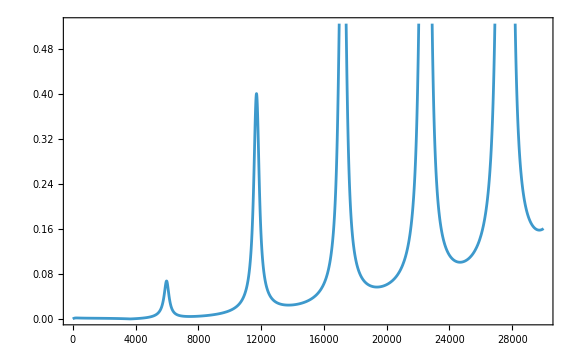

```mathematica
Plot[Abs[Evaluate[(f[x]+δ[x])/π/.sol[50,0.7,0]]-Evaluate[(f[x]+δ[x])/π/.sol[50,0.7,10^-7]]],{x,0,30000},Frame->True,LabelStyle->style,Frame->True,FrameLabel->{MaTeX["t"],MaTeX["\\text{Dephasing (in radians)}"]},ImageSize->Large]
```